```mathematica
k5evos = ;
```

#### Code

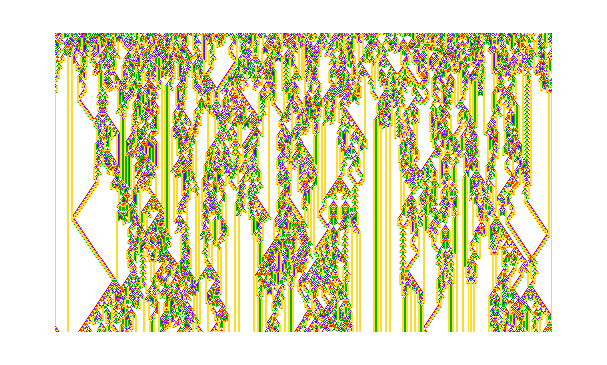

```mathematica
ArrayPlot[CellularAutomaton[#[[1]], RandomInteger[4, 500], 300], ColorRules->colorrules]&/@ Select[k5evos, Last[#]>100&][[{16}]]
```

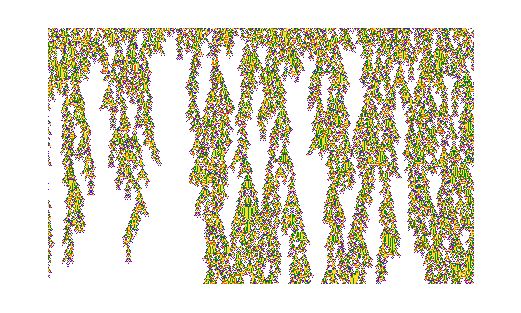
```mathematica
Position[, -Graphics-]
```

{}

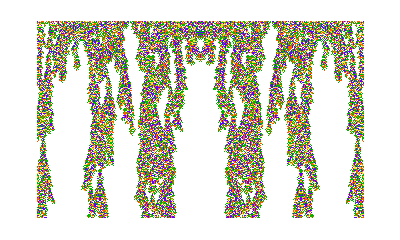
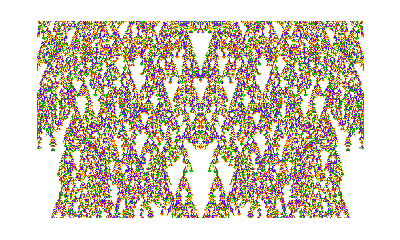
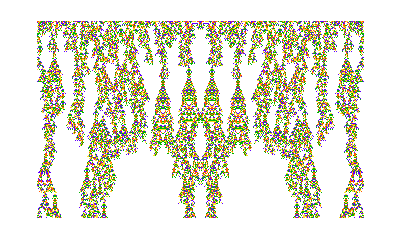
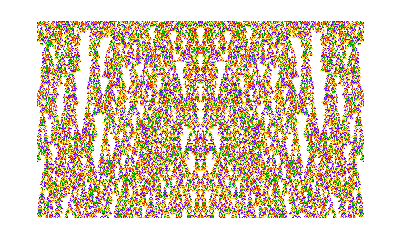
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[#[[1]], Join[#, Reverse[#]]&@RandomInteger[4, 250], 300], ColorRules->colorrules]&/@ Select[k5evos, Last[#]>100&]
```

```mathematica
k5evos2 = ;
```

```mathematica
Length[k5evos2]
```

91

```mathematica
SeedRandom[333223];ArrayPlot[CellularAutomaton[#[[1]], RandomInteger[4, 500], 300], ColorRules->colorrules]&/@RandomSample[ Select[k5evos2, Last[#]>100&], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

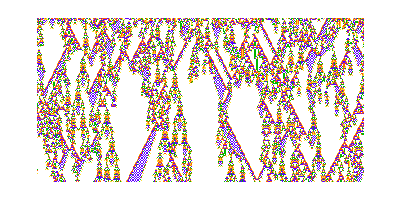

```mathematica
ArrayPlot[CellularAutomaton[#, RandomInteger[4, 400], 200], ColorRules->colorrules]&@{59803220162732970934641323604521097246013443679708480699839552922770071179659424262615,5,1}
```

```mathematica
SeedRandom[333223];RandomSample[ Select[k5evos2, Last[#]>100&], 10][[1, 1]]
```

{59803220162732970934641323604521097246013443679708480699839552922770071179659424262615,5,1}

#### Nice rules

```mathematica
SeedRandom[333223];ArrayPlot[CellularAutomaton[#, RandomInteger[4, 400], 200], ColorRules->colorrules]&@{59803220162732970934641323604521097246013443679708480699839552922770071179659424262615,5,1}
```

-Graphics-

```mathematica
Select[k5evos, Last[#]>100&][[16, 1]]
```

```mathematica
SeedRandom[333223];ArrayPlot[CellularAutomaton[#, RandomInteger[4, 400], 200], ColorRules->colorrules]&@Select[k5evos, Last[#]>100&][[16, 1]]
```

-Graphics-

```mathematica
Select[DeleteCases[rf2dss2,Except[_Association]], #fitness==20949&]
```

{<|RuleNumber→331795689060510718448803690668827312464,Colors→4,fitness→20949|>}

```mathematica
ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119], ColorRules->colorrules]&@<|"RuleNumber"->331795689060510718448803690668827312464,"Colors"->4,"fitness"->20949|>
```

-Graphics-

#### More code

```mathematica
SeedRandom[333445];
rf2dss2 = ParallelMap[Module[{ca, blocks, tots},ca = CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];
tots = Map[Total[#, 2]&, blocks, {2}];
Append[#, "fitness"->Total[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], 2]]]&, Table[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"], 1000]];
```

Get::noopen: Cannot open CloudObject`.

Function::slot1: (Module[{ca,blocks,tots},ca=CellularAutomaton[{#RuleNumber,4,1},RandomInteger[3,200],119];blocks=Partition[ca,{20,20}];tots=Map[Total[Slot[«1»],2]&,blocks,{2}];Append[#1,fitness→Total[Append[«2»]+Abs[«1»],2]]]&)[$Failed[{4,1},Quiescent→True,Type→Symmetric]] is expected to have an Association as the first argument.

CellularAutomaton::nocol: Since position 2 of rule specification {#RuleNumber,4,1} is not {}, position 1 must be an integer or a pure Boolean function.

Partition::pdep: Depth 2 requested in object with dimensions {3}.

CellularAutomaton::nspecnl: Rule specification 5+#RuleNumber should be an Integer, a List, a pure Boolean function, a String or an Association.

Partition::pdep: Depth 2 requested in object with dimensions {3}.

Abs::argx: Abs called with 2 arguments; 1 argument is expected.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Differences[CellularAutomaton[5+#RuleNumber,309,119],0],{0,0}].

Function::slot1: (Module[{ca,blocks,tots},ca=CellularAutomaton[{#RuleNumber,4,1},RandomInteger[3,200],119];blocks=Partition[ca,{20,20}];tots=Map[Total[Slot[«1»],2]&,blocks,{2}];Append[#1,fitness→Total[Append[«2»]+Abs[«1»],2]]]&)[$Failed[{4,1},Quiescent→True,Type→Symmetric]] is expected to have an Association as the first argument.

CellularAutomaton::nocol: Since position 2 of rule specification {#RuleNumber,4,1} is not {}, position 1 must be an integer or a pure Boolean function.

Partition::pdep: Depth 2 requested in object with dimensions {3}.

CellularAutomaton::nspecnl: Rule specification 5+#RuleNumber should be an Integer, a List, a pure Boolean function, a String or an Association.

Partition::pdep: Depth 2 requested in object with dimensions {3}.

Abs::argx: Abs called with 2 arguments; 1 argument is expected.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Differences[CellularAutomaton[5+#RuleNumber,301,119],0],{0,0}].

Get::noopen: Cannot open CloudObject`.

Function::slot1: (Module[{ca,blocks,tots},ca=CellularAutomaton[{#RuleNumber,4,1},RandomInteger[3,200],119];blocks=Partition[ca,{20,20}];tots=Map[Total[Slot[«1»],2]&,blocks,{2}];Append[#1,fitness→Total[Append[«2»]+Abs[«1»],2]]]&)[$Failed[{4,1},Quiescent→True,Type→Symmetric]] is expected to have an Association as the first argument.

CellularAutomaton::nocol: Since position 2 of rule specification {#RuleNumber,4,1} is not {}, position 1 must be an integer or a pure Boolean function.

Partition::pdep: Depth 2 requested in object with dimensions {3}.

CellularAutomaton::nspecnl: Rule specification 5+#RuleNumber should be an Integer, a List, a pure Boolean function, a String or an Association.

Partition::pdep: Depth 2 requested in object with dimensions {3}.

Abs::argx: Abs called with 2 arguments; 1 argument is expected.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Differences[CellularAutomaton[5+#RuleNumber,314,119],0],{0,0}].

```mathematica
SeedRandom[222222];Quiet[Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119], ColorRules->colorrules], Text[#fitness]]&/@Most[GatherBy[SortBy[rf2dss2, #fitness&], Round[#fitness, 500]&][[All, 1]]]]
```

{-Graphics-336,-Graphics-969,-Graphics-1274,-Graphics-1758,-Graphics-2261,-Graphics-2751,-Graphics-3256,-Graphics-3750,-Graphics-4255,-Graphics-4755,-Graphics-5252,-Graphics-5762,-Graphics-6269,-Graphics-6755,-Graphics-7263,-Graphics-7802,-Graphics-8252,-Graphics-8770,-Graphics-9251,-Graphics-9759,-Graphics-10325,-Graphics-10768,-Graphics-11260,-Graphics-11845,-Graphics-12514,-Graphics-12764,-Graphics-13269,-Graphics-13794,-Graphics-14603,-Graphics-15517,-Graphics-15770,-Graphics-16819,-Graphics-17449,-Graphics-19225,-Graphics-19523,-Graphics-20949,-Graphics-21674}

```mathematica
rf2dss2[[2;;]]
```

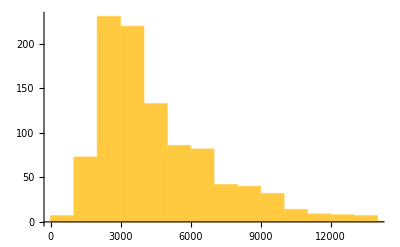

```mathematica
Histogram[DeleteCases[rf2dss2,Except[_Association]][[2;;-2,"fitness"]]]
```

```mathematica
SeedRandom[33235];Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119], ColorRules->colorrules], Text[#fitness]]&/@RandomSample[Select[DeleteCases[rf2dss2,Except[_Association]], #fitness>4000&], 30]
```

{-Graphics-9104,-Graphics-4512,-Graphics-7041,-Graphics-8524,-Graphics-6687,-Graphics-7264,-Graphics-4313,-Graphics-8371,-Graphics-8468,-Graphics-4356,-Graphics-12902,-Graphics-5023,-Graphics-9449,-Graphics-5208,-Graphics-6085,-Graphics-8608,-Graphics-5830,-Graphics-6039,-Graphics-5641,-Graphics-7021,-Graphics-4525,-Graphics-5141,-Graphics-7194,-Graphics-5762,-Graphics-4668,-Graphics-11106,-Graphics-6345,-Graphics-5446,-Graphics-9018,-Graphics-7013}

```mathematica
Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119], ColorRules->colorrules], Text[#fitness]]&/@Select[DeleteCases[rf2dss2,Except[_Association]], #fitness==20949&]
```

{-Graphics-20949}

```mathematica
SeedRandom[333445];
rf2dss2 = ParallelMap[Module[{ca, blocks, tots},ca = CellularAutomaton[{#RuleNumber, 4, 1}, RandomInteger[3, 200], 119];
blocks=Partition[ca,{20, 20}];
tots = Map[Total[#, 2]&, blocks, {2}];
Append[#, "fitness"->Total[Append[Abs[Differences[tots]], Table[0, Length[tots[[1]]]]] + Abs[Append[Differences[#], 0]&/@ tots], 2]]]&, Table[ResourceFunction["RandomCA"][{4, 1}, "Quiescent"->True, "Type"->"Symmetric"], 1000]];
```

#### Example images

Wide:

```mathematica
SeedRandom[333225];ArrayPlot[CellularAutomaton[#, RandomInteger[3, 200], 119], ColorRules->colorrules, ImageSize->500]&@ {59803220162732970934641323604521097246013443679708480699839552922770071179659424262615,5,1}
```

-Graphics-

```mathematica
SeedRandom[333220];ArrayPlot[CellularAutomaton[#, RandomInteger[3, 200], 119], ColorRules->colorrules, ImageSize->500]&@ {894304535182982589660217363651363232120273916790513941661973631574068570531809823773165,5,1}
```

-Graphics-

```mathematica
SeedRandom[333220];ArrayPlot[CellularAutomaton[#, RandomInteger[3, 200], 119], ColorRules->colorrules, ImageSize->500]&@ {331795689060510718448803690668827312464, 4, 1}
```

-Graphics-

Narrow:

```mathematica
SeedRandom[333228];ArrayPlot[CellularAutomaton[#, RandomInteger[3, 100], 240], ColorRules->colorrules]&@ {59803220162732970934641323604521097246013443679708480699839552922770071179659424262615,5,1}
```

-Graphics-

```mathematica
SeedRandom[333226];ArrayPlot[CellularAutomaton[#, RandomInteger[3, 100], 240], ColorRules->colorrules]&@ {894304535182982589660217363651363232120273916790513941661973631574068570531809823773165,5,1}
```

-Graphics-

```mathematica
SeedRandom[333226];ArrayPlot[CellularAutomaton[#, RandomInteger[3, 100], 240], ColorRules->colorrules]&@ {331795689060510718448803690668827312464, 4, 1}
```

-Graphics-